```mathematica
<<MT`;
Install[StringJoin[ParentDirectory@ParentDirectory@NotebookDirectory[],"/Cuba-4.2.2/Vegas"]];
Install[StringJoin[ParentDirectory@ParentDirectory@NotebookDirectory[],"/Cuba-4.2.2/Cuhre"]];
Install[StringJoin[ParentDirectory@ParentDirectory@NotebookDirectory[],"/Cuba-4.2.2/Divonne"]];
Install[StringJoin[ParentDirectory@ParentDirectory@NotebookDirectory[],"/Cuba-4.2.2/Suave"]];
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

ToFileName::strse: A string or list of strings is expected at position 1 in ToFileName[{$HPLPath},MinimalSet2.m].

FileType::badfile: The specified argument, ToFileName[{$HPLPath},MinimalSet2.m], should be a valid string or File object.

ToFileName::strse: A string or list of strings is expected at position 1 in ToFileName[{$HPLPath},MinimalSet3.m].

FileType::badfile: The specified argument, ToFileName[{$HPLPath},MinimalSet3.m], should be a valid string or File object.

ToFileName::strse: A string or list of strings is expected at position 1 in ToFileName[{$HPLPath},MinimalSet4.m].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FileType::badfile: The specified argument, ToFileName[{$HPLPath},MinimalSet4.m], should be a valid string or File object.

General::stop: Further output of FileType::badfile will be suppressed during this calculation.

StringTake::take: Cannot take positions 1 through -3 in "".

StringJoin::string: String expected at position 2 in Rules for minimal set loaded for weights: <>StringTake[,{1,-3}]<>..

Rules for minimal set loaded for weights: <>StringTake[,{1,-3}]<>.

StringTake::take: Cannot take positions 1 through -3 in "".

StringJoin::string: String expected at position 2 in Rules for minimal set for + - weights loaded for weights: <>StringTake[,{1,-3}]<>..

Rules for minimal set for + - weights loaded for weights: <>StringTake[,{1,-3}]<>.

Table of MZVs loaded up to weight Null

Table of values at I loaded up to weight Null

Get::stream: ToFileName[{$HPLPath},nmzv.m] is not a string, SocketObject, InputStream[ ] or OutputStream[ ].

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

MT 1.0 © 2011-2013 by Alexey Pak and Takahiro Ueda, TTP KIT Karlsruhe

Table of MTs loaded up to weight 6.

Table of inverse MTs loaded up to weight 6.

See ?MT`* for a list of functions.

-π^2/12-(3 x)/4+(2 π^2 x)/3+(3 x^2)/4-(3 π^2 x^2)/4-3/2 x HPL[{0},x]+1/6 π^2 x HPL[{0},x]+11/4 x^2 HPL[{0},x]-1/6 π^2 x^2 HPL[{0},x]+3/4 HPL[{1},x]-7/2 x HPL[{1},x]+1/6 π^2 x HPL[{1},x]+11/4 x^2 HPL[{1},x]-1/6 π^2 x^2 HPL[{1},x]+1/2 HPL[{2},x]-4 x HPL[{2},x]+9/2 x^2 HPL[{2},x]-x HPL[{3},x]+x^2 HPL[{3},x]-x HPL[{0,0},x]+3/2 x^2 HPL[{0,0},x]+1/2 HPL[{1,0},x]-2 x HPL[{1,0},x]+3/2 x^2 HPL[{1,0},x]+3/2 HPL[{1,1},x]-6 x HPL[{1,1},x]+9/2 x^2 HPL[{1,1},x]-x HPL[{1,2},x]+x^2 HPL[{1,2},x]-x HPL[{2,0},x]+x^2 HPL[{2,0},x]-3 x HPL[{2,1},x]+3 x^2 HPL[{2,1},x]-x HPL[{1,1,0},x]+x^2 HPL[{1,1,0},x]-3 x HPL[{1,1,1},x]+3 x^2 HPL[{1,1,1},x]+2 x Zeta[3]-2 x^2 Zeta[3]

0.839297

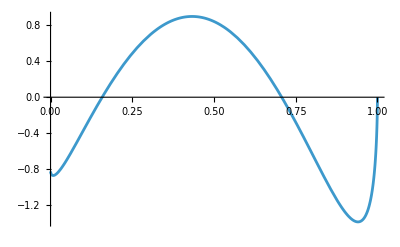

```mathematica
MyF[x_]:=x*(1-x);
MyConv=Convolution[PlusDistribution[0,1-x],PlusDistribution[1,1-x],x];
MyResult=Convolution[MyF[x],MyConv,x]
MyResult/.x->0.5
Plot[MyResult/.x->t,{t,0,1}]
```

```mathematica
MyPlus[k_,x_]:=Log[1-x]^k/(1-x);
MyHeavy[t_]:=If[t>=0,1,0];
MyIntegrand[v_,w_]:=MyPlus[0,v]*MyPlus[1,w]*(
MyHeavy[v*w-x]*MyF[x/(w*v)]/(w*v)
-MyHeavy[v-x]*MyF[x/v]/(v)
-MyHeavy[w-x]*MyF[x/w]/(w)
+MyF[x]
)/.x->0.5
Cuhre[MyIntegrand[v,w],{v,0,1},{w,0,1},Verbose->0,MaxPoints->100000]
Vegas[MyIntegrand[v,w],{v,0,1},{w,0,1},Verbose->0,MaxPoints->100000]
Divonne[MyIntegrand[v,w],{v,0,1},{w,0,1},Verbose->0,MaxPoints->100000]
Suave[MyIntegrand[v,w],{v,0,1},{w,0,1},Verbose->0,MaxPoints->100000]
NIntegrate[MyIntegrand[v,w],{v,0,1},{w,0,1}]
```

Cuhre::success: Needed 17745 function evaluations on 137 subregions.

{{0.83928,0.000830898,1.11022×10^-16}}

Vegas::accuracy: Desired accuracy was not reached within 104500 function evaluations.

{{0.839197,0.00224284,3.33067×10^-16}}

Power::infy: Infinite expression 1/0. encountered.

Divonne::badsample: MyIntegrand[v,w] is not a real-valued function at {1.,1.}.

$Failed

Suave::success: Needed 40000 function evaluations on 40 subregions.

{{0.839188,0.000829124,1.}}

0.839297